```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
```

## Main implementation

Mutation rules are from D. Djokovic, “Closures of Conjugacy Classes in Classical Real Linear Lie Groups. II”, Transactions of the American Mathematical Society 270,1 (1982).

Eq. (8.1): g^ϵ(m)+g^(-ϵ)(n)→g^(-ϵ)(m-1)+g^ϵ(n+1)     m <=n
Eq. (8.2): g^ϵ(m)+g^ϵ(n)→g^ϵ(m-2)+g^ϵ(n+2)             1<m<=n
Eq. (8.3): g_ϵ(m)+g_{-ϵ}(n)→g_{-ϵ}(m-1)+g_ϵ(n+1)    m<=n

```mathematica
(*find values of m and ϵ from term=mϵ*)
parseTerm[term_String]:=Module[{m,eps},
If[
StringTake[term,-1]=="+",m=ToExpression[StringDrop[term,-1]];
eps="+";,m=ToExpression[StringDrop[term,-1]];
eps="-";];
{m,eps}]
```

```mathematica
(*find term=mϵ given m and ϵ*)
makeTerm[m_Integer,eps_String]:=ToString[m]<>eps
```

```mathematica
(*printing node labels for chromosom_list*)
formatChromosome[chromosome_List]:=StringRiffle[chromosome,{"{"," , ","}"}]
```

```mathematica
(*sort elements of chormosome list to prevent duplication in nodes*)
sortChromosomeCompact[chromosome_List]:=Module[{groupedByValue,sortedGroups},groupedByValue=GatherBy[chromosome,ToExpression[StringDrop[#,-1]]&];
sortedGroups=Map[SortBy[#,If[StringEndsQ[#,"+"],0,1]&]&,groupedByValue];
sortedGroups=SortBy[sortedGroups,-ToExpression[StringDrop[#[[1]],-1]]&];
Flatten[sortedGroups]]
```

```mathematica
(*filter out 0+ and 0- terms from mutated results*)
filterZeroTerms[chromosome_List]:=Select[chromosome,!StringMatchQ[#,"0+"|"0-"]&]
```

```mathematica
(*imposing the conversiong_ϵ(n) to g^ϵ'(n) using g_ϵ(n)=g^{(-1)^{n-1}ϵ}(n); Note that all final terms are in g^ϵ format*)
convertToGSubEpsilon[n_Integer,currentEpsilon_String]:=Module[{signFactor},signFactor=(-1)^(n-1);If[signFactor==1,currentEpsilon,
If[currentEpsilon=="+","-","+"]]]
```

```mathematica
(*apply mutations given by Eqs. (8.1-8.3) above*)
applyMutation[chromosome_List,mutationType_String,m_Integer,n_Integer]:=Module[{results={},newChromosome,term1,term2,eps1,eps2,newTerm1,newTerm2,remainingTerms,m1,m2},If[MemberQ[{"8.1","8.3"},mutationType]&&m>n,Print["Error: For mutation types 8.1 and 8.3, must have m ≤ n"];
Return[{}]];
If[mutationType=="8.2"&&(m<=1||m>n),Print["Error: For mutation type 8.2, must have 1 < m ≤ n"];
Return[{}]];
Do[term1=chromosome[[i]];
term2=chromosome[[j]];
{m1,eps1}=parseTerm[term1];
{m2,eps2}=parseTerm[term2];
(*Check if this pair matches the mutation pattern*)If[mutationType=="8.1",If[((m1==m&&m2==n&&eps1!=eps2)||(m1==n&&m2==m&&eps1!=eps2)),remainingTerms=Delete[chromosome,{{i},{j}}];
If[m1==m,
newEps2=eps1;
newEps1 =eps2;
newTerm1=makeTerm[m-1,newEps1];
newTerm2=makeTerm[n+1,newEps2];,
newEps2=eps2;
newEps1 =eps1;
newTerm1=makeTerm[m-1,newEps1];
newTerm2=makeTerm[n+1,newEps2];];
newChromosome=Join[remainingTerms,{newTerm1,newTerm2}];
AppendTo[results,newChromosome];]];
If[mutationType=="8.2",If[((m1==m&&m2==n&&eps1==eps2)||(m1==n&&m2==m&&eps1==eps2)),remainingTerms=Delete[chromosome,{{i},{j}}];
newTerm1=makeTerm[m-2,eps1];
newTerm2=makeTerm[n+2,eps1];
newChromosome=Join[remainingTerms,{newTerm1,newTerm2}];
AppendTo[results,newChromosome];]];
If[mutationType=="8.3",
Module[{gSubEpsM,gSubEpsN,requiredEpsM,requiredEpsN},gSubEpsM=convertToGSubEpsilon[m1,eps1];
gSubEpsN=convertToGSubEpsilon[m2,eps2];If[((m1==m&&m2==n&&gSubEpsM!=gSubEpsN)||(m1==n&&m2==m&&gSubEpsM!=gSubEpsN)),remainingTerms=Delete[chromosome,{{i},{j}}];
If[m1==m,Module[{newEps1,newEps2},newEps1=If[(-1)^(m-2)==1,If[gSubEpsM=="+","-","+"],gSubEpsM  ];
newEps2=If[(-1)^n==1,gSubEpsM,If[gSubEpsM=="+","-","+"]  ];
newTerm1=makeTerm[m-1,newEps1];
newTerm2=makeTerm[n+1,newEps2];];,Module[{newEps1,newEps2},newEps1=If[(-1)^(m-2)==1,If[gSubEpsN=="+","-","+"],gSubEpsN];
newEps2=If[(-1)^n==1,gSubEpsN,If[gSubEpsN=="+","-","+"]];
newTerm1=makeTerm[m-1,newEps1];
newTerm2=makeTerm[n+1,newEps2];];];
newChromosome=Join[remainingTerms,{newTerm1,newTerm2}];
AppendTo[results,newChromosome];]]];,{i,1,Length[chromosome]-1},{j,i+1,Length[chromosome]}];
Map[filterZeroTerms,results]]
```

```mathematica
(*find all possible mutations from a given chromosome*)findAllMutations[chromosome_List,maxValue_Integer:40]:=Module[{allMutations={},results},Do[Do[Do[If[mutationType=="8.2"&&m<=1,Continue[]];If[MemberQ[{"8.1","8.3"},mutationType]&&m<0, Continue[]];
results=applyMutation[chromosome,mutationType,m,n];
If[Length[results]>0,AppendTo[allMutations,{mutationType,m,n,results}]];,{n,m,maxValue}],{m,1,maxValue}],{mutationType,{"8.1","8.2","8.3"}}];
allMutations]
```

```mathematica
(*create directed mutation tree: inputs(startchromosoms, maxdepth of tree, max_m)*)
createDirectedMutationTree[startChromosome_List,maxDepth_Integer:10,maxValue_Integer:40]:=Module[{currentLevel,allNodes,allEdges,depth,nodeCounter,nodeMap,nodeLevels},currentLevel={startChromosome};
allNodes={startChromosome};
allEdges={};
nodeCounter=1;
nodeMap=<|ToString[startChromosome]->1|>;
nodeLevels=<|1->0|>;For[depth=0,depth<maxDepth,depth++,Module[{nextLevel},nextLevel={};
Do[Module[{mutations,parentKey,parentID},parentKey=ToString[sortChromosomeCompact[chromosome]];
parentID=nodeMap[parentKey];
mutations=findAllMutations[sortChromosomeCompact[chromosome],maxValue];
Do[Module[{mutationType,m,n,results},{mutationType,m,n,results}=mutation;
Do[Module[{childKey,childID},childKey=ToString[sortChromosomeCompact[result]];
If[!KeyExistsQ[nodeMap,childKey],AppendTo[allNodes,sortChromosomeCompact[result]];
nodeMap[childKey]=++nodeCounter;
nodeLevels[nodeCounter]=depth+1;];
childID=nodeMap[childKey];AppendTo[allEdges,<|"from"->parentID,"to"->childID,"mutationType"->mutationType,"m"->m,"n"->n,"fromLevel"->depth,"toLevel"->depth+1,"label"->mutationType<>"\n(m="<>ToString[m]<>",n="<>ToString[n]<>")"|>];
AppendTo[nextLevel,result];],{result,results}]],{mutation,mutations}]],{chromosome,currentLevel}];
currentLevel=DeleteDuplicates[nextLevel];]];
{allNodes,Select[allEdges,!MissingQ[#["from"]]&],nodeMap,nodeLevels}]
```

```mathematica
(*create mutation tree with given depth and max m value. edge labels are mutation equation and by default is not shown*)
createGraphMutationTree[startChromosome_List,maxDepth_Integer:10,maxValue_Integer:40,showEdgeLabels_:False]:=Module[{nodes,edges,nodeMap,nodeLevels,graphEdges,vertexLabels,uniqueEdges,edgeLabels,graphOptions},{nodes,edges,nodeMap,nodeLevels}=createDirectedMutationTree[sortChromosomeCompact[startChromosome],maxDepth,maxValue];
If[Length[edges]==0,Return[Graphics[{Text[Style["No mutations found",FontSize->14],{0,0}]}]]];
graphEdges=Map[DirectedEdge[#["from"],#["to"]]&,edges];uniqueEdges=DeleteDuplicates[graphEdges];
vertexLabels=Table[i->formatChromosome[nodes[[i]]],{i,Length[nodes]}];
If[showEdgeLabels,edgeLabels=Table[DirectedEdge[edges[[i]]["from"],edges[[i]]["to"]]->edges[[i]]["label"],{i,Length[edges]}];
edgeLabels=DeleteDuplicatesBy[edgeLabels,First];
graphOptions={VertexLabels->vertexLabels,(*VertexLabelStyle->20,*)EdgeLabels->edgeLabels,EdgeStyle->Blue,VertexStyle->Black,GraphLayout->"LayeredDigraphEmbedding",PlotLabel->Style["Mutation Tree: "<>formatChromosome[startChromosome],Bold,FontSize->17],ImageSize->Large,VertexSize->Small},graphOptions={VertexLabels->vertexLabels,(*VertexLabelStyle->20,*)EdgeStyle->Blue,VertexStyle->Black,GraphLayout->"LayeredDigraphEmbedding",PlotLabel->Style["Mutation Tree: "<>formatChromosome[startChromosome],Bold,FontSize->17],ImageSize->Large,VertexSize->Small}];
ReverseGraph[Graph[uniqueEdges,Sequence@@graphOptions]]]
```

```mathematica
(*show Graph versions with flexible parameters*)
showMutationTrees[startChromosome_List,maxDepth_Integer:10,maxValue_Integer:10]:=Module[{hasseDiagram,graphVersion},Print["MUTATION TREES - COMPARISON"];
Print["Starting chromosome: ",formatChromosome[sortChromosomeCompact[startChromosome]]];
Print["Max depth: ",maxDepth,", Max value: ",maxValue];
graphVersion=createGraphMutationTree[sortChromosomeCompact[startChromosome],maxDepth,maxValue];
Print[graphVersion];
{hasseDiagram,graphVersion}]
```

## Examples :

MUTATION TREES - COMPARISON

Starting chromosome: {1+ , 1+ , 1- , 1-}

Max depth: 10, Max value: 10

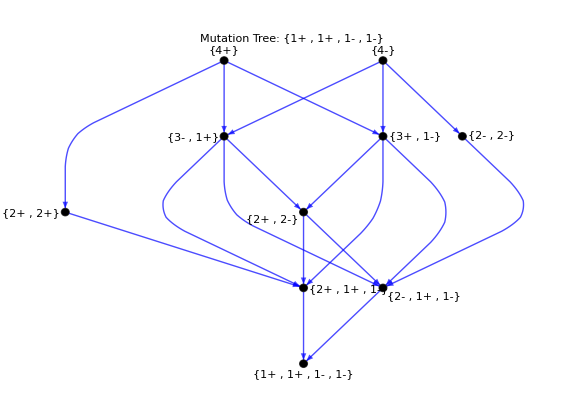

```mathematica
X={"1+","1-","1+", "1-"};
showMutationTrees[X, 10, 10];
```

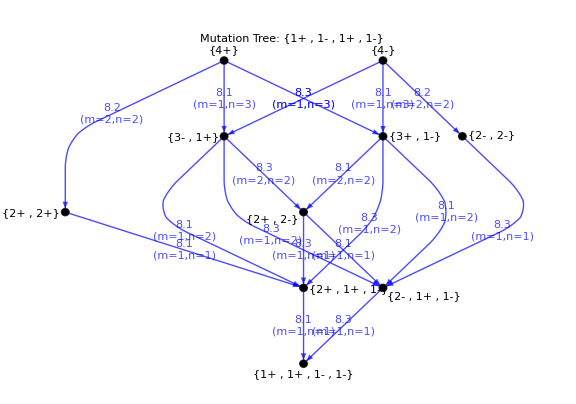

```mathematica
createGraphMutationTree[X,10,10,True]
```

MUTATION TREES - COMPARISON

Starting chromosome: {1+ , 1+ , 1+ , 1- , 1-}

Max depth: 10, Max value: 10

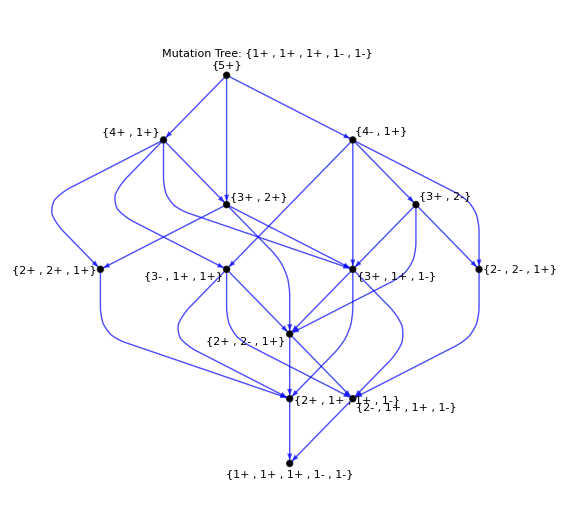

```mathematica
X={"1+","1+","1+", "1-", "1-"};
showMutationTrees[X, 10, 10];
```

MUTATION TREES - COMPARISON

Starting chromosome: {1+ , 1+ , 1+ , 1+ , 1+ , 1+ , 1- , 1- , 1-}

Max depth: 2, Max value: 10

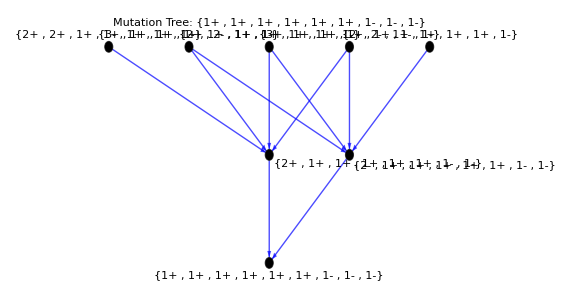

```mathematica
showMutationTrees[X, 2, 10];
```